/Users/Roman/Desktop/рабочая/

{{0,4},{1,8},{2,4},{3,0},{4,0}}

0.004185

{KernelObject[…],KernelObject[…]}

/Users/Roman/Desktop/рабочая/result.txt

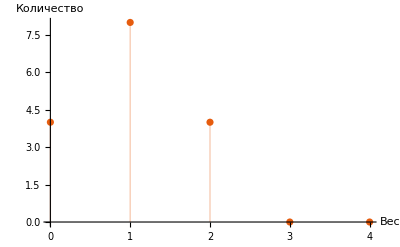

```mathematica
filepath=NotebookDirectory[](* файлы weight spectrum.nb, data.txt и result.txt находятся в одной папке*)
basis=ToExpression[(Characters@DeleteDuplicates[Import[FileNameJoin[{filepath,"data.txt"}],"Lines"]])];
ws=WeightSpectrumGrayCode[basis]

(* компиляция вычисления весового спектра *)
(* WeightSpectrum=
Compile[{{basevectors,_Integer,2}},
Module[{
n=Dimensions[basevectors][[-1]], (* размерность векторов *)
k=Length[basevectors],  (* количество векторов *)
s=Table[0,{i,0,Dimensions[basevectors][[-1]]}]      
 (* создается результирующий список,который содержит количество всех векторов с определенным весом и заполняется нулями. 
индекс в списке - это и есть вес вектора,значение элемента по индексу - есть количество векторов с весом равным индексу *)
},
Do[
With[{l=Total[Mod[Total[IntegerDigits[b,2,k]*basevectors],2]]+1},
(* рассчитывается вес для определенного набора из bi-ых и индекс для полученного веса увеличивается на единицу *)
s[[l]]=s[[l]]+1],
{b,0,2^k-1}];
Return[Transpose[{Range[0,Last[Dimensions[basis]]],s}]]
]
];   *)

(* компиляция вычисления весового спектра с использованием кода Грея *)
WeightSpectrumGrayCode=
Compile[{{basevectors,_Integer,2}},
Module[{
n=Dimensions[basevectors][[-1]], (* размерность векторов *)
k=Length[basevectors], (* количество векторов *)
s=Table[0,{n+1}],       (* создается результирующий список, который содержит количество всех векторов с определенным весом и заполняется нулями *)
currentVector=Table[0,{n}],
(* первая комбинация всегда {0,0,..} *)
m=0,l=0
},
(* точно известно, что в спектре у 0 будет вес больше или равен 1, так как первая линейная комбинация всегда является нулевым вектором *)
s[[1]]=1;
(* предположим, что по списку bi разница между представлением bk и 
bk+1 всего в нескольких битах, тогда можно получить линейную комбинацию 
с номером k и прибавить к ней только те базисные вектора, 
индекс которых совпадает с номерами отличающихся бит между k и 
k+1. результатом будет линейная комбинация k+1 *)
Do[
(*позиция изменившегося бита*)
m=Log2[BitAnd[-1-b,b+1]]+1;
(* здесь нет полного сложения векторов, а только прибавление разницы *)
currentVector=BitXor[currentVector,basevectors[[m]]];
(*подсчет веса*)
l=Total[currentVector]+1;
s[[l]]=s[[l]]+1,
{b,0,2^k-2}
];
Return[Transpose[{Range[0,Last[Dimensions[basis]]],s}]]
]
]; 
(* разделим диапазон всех комбинаций на равные части в зависимости от количества доступных ядер,то есть в результате каждое ядро возвращает частичный спектр *)
partition[{i1_Integer,iN_Integer},n_Integer]:=
With[{dn=Round[(iN-i1+1)/n]},
Join[
{{i1,i1+dn-1}},
Table[{dn*(i-1),i*dn-1},{i,2,n-1}],
{{(n-1)*dn,iN}}
]
]
(* отправляем эти вычисления на разные ядра *)
WeightSpectrumCodeParallel[basis:{{__Integer}..}]:=
With[{
kernels=(If[Kernels[]==={},LaunchKernels[]];Kernels[]),
parts=partition[{0,2^Length[basis]-1},Length[Kernels[]]]
},
Total[WaitAll[Table[
ParallelEvaluate[ParallelSubmit[WeightSpectrumGrayCode[basis,parts[[$KernelID]]]],kernel],
{kernel,kernels}
]]]
]
(* показать время вычислений *)
AbsoluteTiming[ParallelEvaluate[WeightSpectrumGrayCode[basis]];][[1]]
(* показать все запущенные ядра *)
Kernels[]
(* сохраняем результат в файл result.txt *)
Export[FileNameJoin[{filepath,"result.txt"}], ws,"Table","FieldSeparators"-> "\t"]
(* смотрим на результат в файле *)
SystemOpen[%]
(* визуализируем весовой спектр *)
ListPlot[ws,PlotTheme->"DarkColor",AxesLabel->{"Вес","Количество"},AxesOrigin->{0,0},PlotRange->All,Filling->Bottom]
```